#### TrISAW Bulk

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_TrISAW_All.txt","Table"];
```

```mathematica
data[[1]]
```

{100,0,0,0.36472,0.000099635,0.369087,0.0000728157,0.18458,0.0000681002,0.060409,0.0000380988,0.0115279,0.0000185971,68352000000}

```mathematica
Length[data[[1]]]
```

14

Data:
1 - N
2 - J
3 - h
4 - n2
5 - n2_err
6 - n3
7 - n3_err
8 - n4
9 - n4_err
10 - n5
11 - n5_err
12 - n6
13 - n6_err
14 - steps

#### Графики зависимости отношения числа узлов с k - соседями от J от k

```mathematica
Pal={RGBColor[0.2077043757885766, 0.7464871412445997, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]}
```

{RGBColor[0.2077043757885766, 0.7464871412445997, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]}

-Graphics-

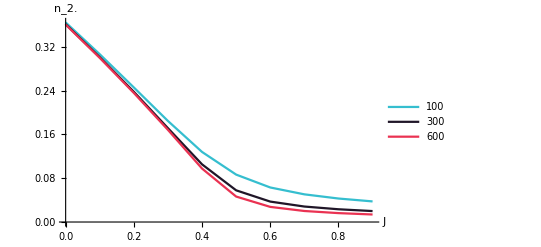
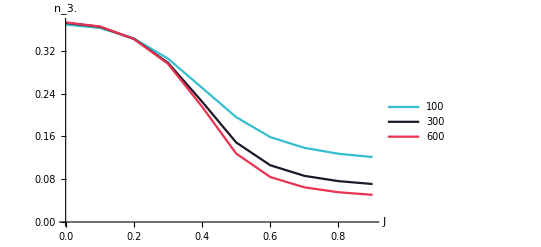
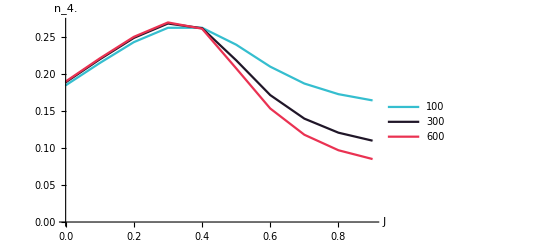
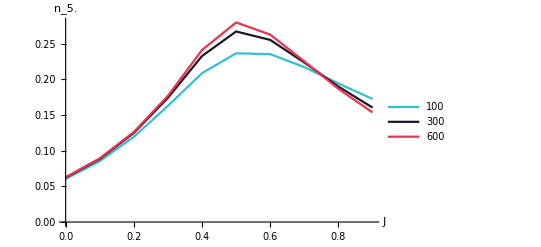
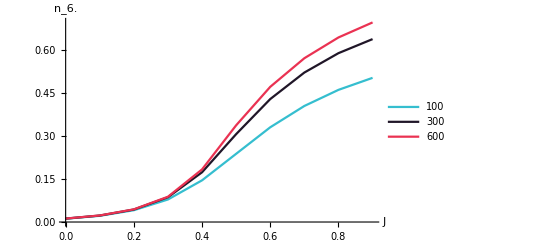

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_TrISAW_All.txt","Table"];
Needs["ErrorBarPlots`"]
Ns=Union[data[[All,1]]];
PlotsAll={};
Font1=20;
Do[
Colors=Pal;
lines={};
Do[
line=Select[data, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
AppendTo[lines,line];
,{n1,Ns}];
plt=ErrorListPlot[lines, PlotLegends->Map[Style[#,Font1]&,Ns],PlotStyle->Colors,Joined->True,PlotRange->All,AxesLabel->{Style["J",Font1],Style[Text[Subscript[n, N[(i)/2]]],Font1]}];
AppendTo[PlotsAll,plt];
,{i,{4,6,8,10,12}}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
i=2;
Do[
Export[StringJoin["TrISAW_Bulk_n",ToString[i],".png"], Show[plt,ImageSize->700,PlotRange->All,AxesOrigin->{0,0},AxesStyle->Directive[Font1]]];
i+=1;
,{plt,PlotsAll}];
Import["C:\\Users\\user\\Documents\\Wolfram Mathematica\\Проект\\Расчёты .nb\\Images\\TrISAW_Bulk_n2.png"]
PlotsAll
```

#### ISAW 3D Bulk

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_TrISAW_All.txt","Table"];
```

```mathematica
data[[1]]
```

{100,0,0,0.36472,0.000099635,0.369087,0.0000728157,0.18458,0.0000681002,0.060409,0.0000380988,0.0115279,0.0000185971,68352000000}

```mathematica
Length[data[[1]]]
```

14

Data:
1 - N
2 - J
3 - h
4 - n2
5 - n2_err
6 - n3
7 - n3_err
8 - n4
9 - n4_err
10 - n5
11 - n5_err
12 - n6
13 - n6_err
14 - steps

#### Графики зависимости отношения числа узлов с k - соседями от J от k

```mathematica
Pal={RGBColor[0.2077043757885766, 0.7464871412445997, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]}
```

{RGBColor[0.2077043757885766, 0.7464871412445997, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]}

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_ISAW_3D_All.txt","Table"];
Needs["ErrorBarPlots`"]
Ns=Union[data[[All,1]]];
PlotsAll={};
Font1=20;
Do[
Colors=Pal;
lines={};
Do[
line=Select[data, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
AppendTo[lines,line];
,{n1,Ns}];

plt=ErrorListPlot[lines, PlotLegends->Map[Style[#,Font1]&,Ns],PlotStyle->Colors,Joined->True,PlotRange->All,AxesLabel->{Style["J",Font1],Style[Text[Subscript[n, N[(i)/2]]],Font1]}];
AppendTo[PlotsAll,plt];
,{i,{4,6,8,10,12}}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
i=2;
Do[
Export[StringJoin["ISAW_3D_Bulk_n",ToString[i],".png"], Show[plt,ImageSize->700,PlotRange->All,AxesOrigin->{0,0},AxesStyle->Directive[Font1]]];
i+=1;
,{plt,PlotsAll}]
```

#### Изменение легенды

{{0.95,0.9},{0.95,0.9},{0.1,0.9},{0.1,0.9},{0.1,0.9}}

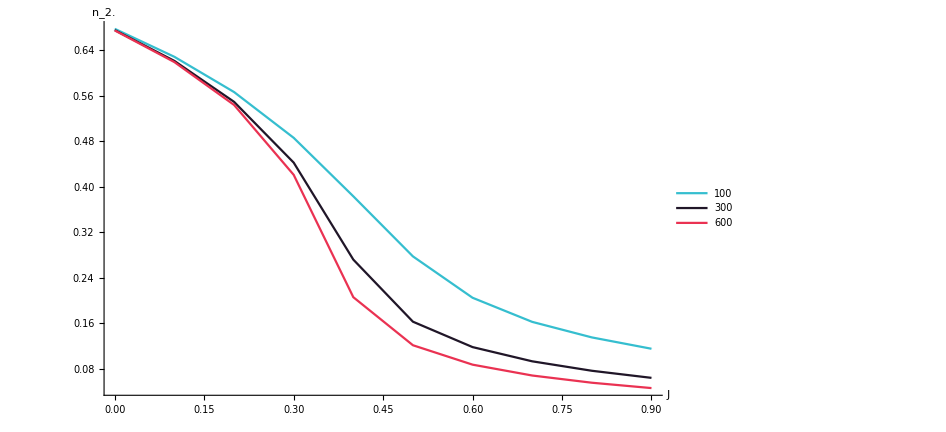

```mathematica
Pal={RGBColor[0.2077043757885766, 0.7464871412445997, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]};
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_ISAW_3D_All.txt","Table"];
Needs["ErrorBarPlots`"]
Ns=Union[data[[All,1]]];
PlotsAll={};
Font1=20;
Do[
Colors=Pal;
Plots={};
Do[
line=Select[data, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
plt=ErrorListPlot[line,PlotStyle->First[Colors],Joined->True,PlotRange->All,AxesLabel->{Style["J",Font1],Style[Text[Subscript[n, N[(i)/2]]],Font1]}];
AppendTo[Plots,plt];
Colors=Delete[Colors,1];
,{n1,Ns}];
AppendTo[PlotsAll,Plots];
,{i,{4,6,8,10,12}}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
i=2;
fp1=Line[{{0.52,0},{0.52,1}}];
fp2=Line[{{0.53,0},{0.53,1}}];
Places={{0.95,0.9},{0.95,0.9},{0.1,0.9},{0.1,0.9},{0.1,0.9}}
Do[
Export[StringJoin["ISAW_3D2_Bulk_n",ToString[i],".png"], Show[Legended[plt,Placed[LineLegend[Pal,Map[Style[#,Font1]&,Ns]],Places[[i-1]]]],ImageSize->700,PlotRange->All,AxesOrigin->{0,0},AxesStyle->Directive[Font1]]];
i+=1;
,{plt,PlotsAll}]
```

```mathematica
Pal={RGBColor[0.2077043757885766, 0.28, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]};
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data1=Import["Geometry_ISAW_3D_All.txt","Table"];
Needs["ErrorBarPlots`"]
Ns=Union[data[[All,1]]];
PlotsAll={};
Font1=30;
Do[
Colors=Pal;
Plots={};
PS=20;
Do[
line=Select[data, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
plt=ErrorListPlot[line,PlotMarkers->{Automatic,PS},PlotStyle->First[Colors],Joined->True,Axes->{False, False}];
AppendTo[Plots,plt];
Colors=Delete[Colors,1];
,{n1,Ns}];
AppendTo[PlotsAll,Plots];
,{i,{4,6,8,10,12}}];
Font1=30;
Font2=Font1*1.3;
IS={900,600};
a2=Show[PlotsAll[[1]],ImageSize->IS,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 2]],Black,Font1]}];
a3=Show[PlotsAll[[2]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 3]],Black,Font2]}];
a4=Show[PlotsAll[[3]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 4]],Black,Font2]}];
a5=Show[PlotsAll[[4]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 5]],Black,Font2]}];
a6=Show[Legended[PlotsAll[[5]],Placed[Framed[LineLegend[Pal,Map[Style[#,Font1]&,Ns],LegendMarkerSize->30]],{0.1,0.8}]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 6]],Black,Font1]}];
a=GraphicsRow[{a3,a4,a5}];
b=GraphicsRow[{a2,a6}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
a=ImageCollage[{a,b},Background->None,ImageSize->1200]
Export["ISAW_3D_Complex.png",a];
```

-Graphics-

```mathematica
Pal={RGBColor[0.2077043757885766, 0.28, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]};
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_TrISAW_All.txt","Table"];
Needs["ErrorBarPlots`"]
Ns=Union[data[[All,1]]];
PlotsAll={};
Font1=30;
Do[
Colors=Pal;
Plots={};
PS=20;
Do[
line=Select[data, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
plt=ErrorListPlot[line,PlotMarkers->{Automatic,PS},PlotStyle->First[Colors],Joined->True,Axes->{False, False}];
AppendTo[Plots,plt];
Colors=Delete[Colors,1];
,{n1,Ns}];
AppendTo[PlotsAll,Plots];
,{i,{4,6,8,10,12}}];
Font1=30;
Font2=Font1*1.3;
IS={900,600};
a2=Show[PlotsAll[[1]],ImageSize->IS,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 2]],Black,Font1]}];
a3=Show[PlotsAll[[2]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 3]],Black,Font2]}];
a4=Show[PlotsAll[[3]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 4]],Black,Font2]}];
a5=Show[PlotsAll[[4]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 5]],Black,Font2]}];
a6=Show[Legended[PlotsAll[[5]],Placed[Framed[LineLegend[Pal,Map[Style[#,Font1]&,Ns],LegendMarkerSize->30]],{0.1,0.8}]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 6]],Black,Font1]}];
a=GraphicsRow[{a3,a4,a5}];
b=GraphicsRow[{a2,a6}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
a=ImageCollage[{a,b},Background->None,ImageSize->1200]
Export["TrISAW_Complex.png",a];
```

-Graphics-

```mathematica
Ns
```

{100,300,600}

```mathematica
Pal={RGBColor[0.2077043757885766, 0.28, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]};
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data2=Import["Geometry_TrISAW_All.txt","Table"];
data1=Import["Geometry_ISAW_3D_All.txt","Table"];
Needs["ErrorBarPlots`"]
Ns=Union[data1[[All,1]]];
PlotsAll={};
Font1=30;
Do[
Colors=Pal;
PS=25;
lines1={};
lines2={};
Do[
line=Select[data1, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
AppendTo[lines1,line];
line=Select[data2, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
AppendTo[lines2,line];
,{n1,Ns}];
PlSt={{Colors[[1]]},{Colors[[2]]},{Colors[[3]]},{Dashed,Colors[[1]]},{Dashed,Colors[[2]]},{Dashed,Colors[[3]]}};
plt1=ErrorListPlot[Join[lines1,lines2],PlotMarkers->{Automatic,PS},PlotStyle->PlSt,Joined->True,Axes->{False, False}];
AppendTo[PlotsAll,plt1];
,{i,{4,6,8,10,12}}];
Font1=30;
Font2=Font1*1.3;
IS={900,600};

a2=Show[PlotsAll[[1]],ImageSize->IS,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 2]],Black,Font1]}];
a3=Show[PlotsAll[[2]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 3]],Black,Font2]}];
a4=Show[PlotsAll[[3]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 4]],Black,Font2]}];
a5=Show[PlotsAll[[4]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 5]],Black,Font2]}];
a6=Show[PlotsAll[[5]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 6]],Black,Font1]}];
a=GraphicsRow[{a3,a4,a5}];
b=GraphicsRow[{a2,a6}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
a=ImageCollage[{a,b},Background->None,ImageSize->1200]
Export["TrISAW_Complex.png",a];
```

-Graphics-

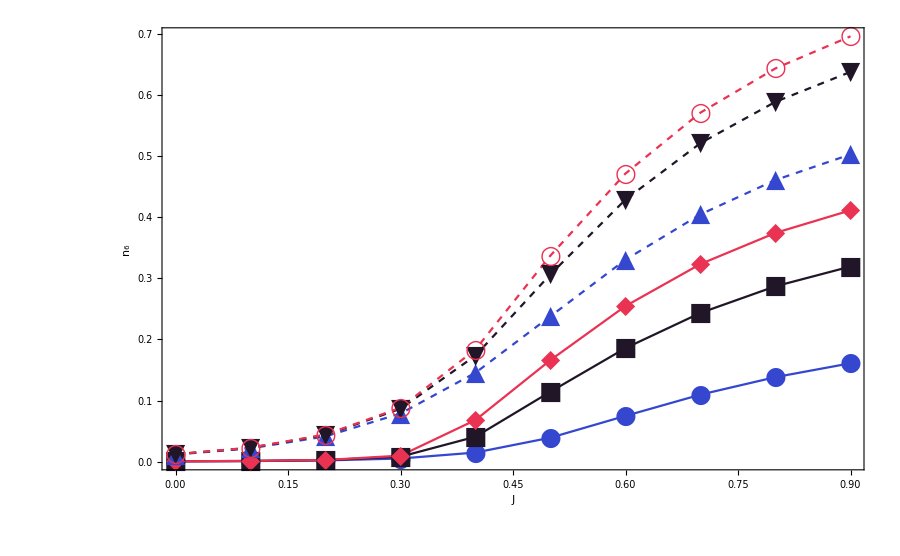

```mathematica
Legend=Map[Style[#,20]&,{"100 3D", "300 3D", "600 3D","100 Triangle","300 Triangle","600 Triangle"}];
a6=Show[Legended[PlotsAll[[5]],LineLegend[Legend]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 6]],Black,Font1]}]
```

```mathematica
lines1={{1,1},{2,2}}
lines2={{3,3},{4,4}}
Join[lines1,lines2]
```

{{1,1},{2,2}}

{{3,3},{4,4}}

{{1,1},{2,2},{3,3},{4,4}}

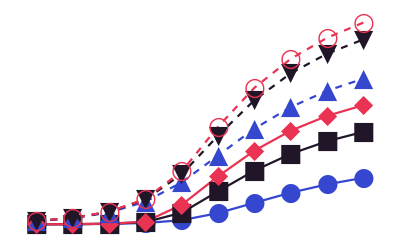

```mathematica
Legended[PlotsAll[[5]],LineLegend[Legend]]
```

```mathematica
LineLegend[Join[Pal,Pal],Legend]
```

Join::heads: Heads List and Dashing at positions 1 and 2 are expected to be the same.

LineLegend[Join[{RGBColor[0.2077043757885766, 0.28, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]},Dashing[{Small,Small}],{RGBColor[0.2077043757885766, 0.28, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]}],{100 3D,300 3D,600 3D,100 Triangle,300 Triangle,600 Triangle}]